## Initialization

### Solution Matrix

```mathematica
n=1;
store={({{t Sin[t]+Cos[t], -Sin[t]}, {Sin[t]-t Cos[t], Cos[t]}}),({{Exp[t], 1}, {-1, Exp[-t]}})};
Ψ[t_]=store[[n]];
```

### Initiali Condition and Coupling Matrix

```mathematica
t0=0;
x[t_]=Ψ[t].{1,1};
x1[t_]=x[t][[1]];
x2[t_]=x[t][[2]];
x0=x[0];
A[t_]= Ψ'[t].Inverse[Ψ[t]];
A[t]//MatrixForm
If[AllTrue[Flatten[A[t0]],NumericQ],{},Abort[]]//Quiet;
```

(1/2 | -ⅇ^t/2
-ⅇ^-t/2 | -1/2)

### Helper Functions

```mathematica
c[A_,B_]=A.B-B.A; (* Commutator *)
```

## Magnus Expansion Terms

### Analytical

```mathematica
Ω=Table[{},{k,1,3}];
success=TimeConstrained[
Block[{$Assumptions=t>0&&{t1|t2|t3}∈Reals},
Ω[[1]]=∫_t0^t A[t1]ⅆt1;
Ω[[2]]=1/2∫_t0^t ∫_t0^t1 c[A[t1],A[t2]]ⅆt2ⅆt1;
Ω[[3]]=1/6∫_t0^t ∫_t0^t1 ∫_t0^t2 (c[A[t1],c[A[t2],A[t3]]]+c[A[t3],c[A[t2],A[t1]]])ⅆt3ⅆt2ⅆt1;
];
Ω=Accumulate[Ω];
S[t_]=Map[MatrixExp[#].x0&,Ω];
x1Magnus[t_]=S[t][[All,1,All]];
x2Magnus[t_]=S[t][[All,2,All]];
,60,"nope"
];
If[success==="nope",
x1Magnus[t_]={0,0,0};
x2Magnus[t_]={0,0,0};
,{}];
success
```

### Coarse Quadrature

```mathematica
Ωapp=Table[{},{k,1,3}];
(*int[f_,t_,a_,b_]:=(b-a)/2((f/.{t->a})+(f/.{t->b}));*)
int[f_,t_,a_,b_]:=(b-a)/6((f/.{t->a})+4(f/.{t->(a+b)/2})+(f/.{t->b}));
Ωapp[[1]]=int[A[t1],t1,t0,t];
Ωapp[[2]]=1/2 int[int[c[A[t1],A[t2]],t2,t0,t1],t1,t0,t];
Ωapp[[3]]=1/6 int[int[int[c[A[t1],c[A[t2],A[t3]]]+c[A[t3],c[A[t2],A[t1]]],t3,t0,t2],t2,t0,t1],t1,t0,t];
Ωapp=Accumulate[Ωapp];
Sapp[t_]=Map[MatrixExp[#].x0&,Ωapp];
x1app[t_]=Sapp[t][[All,1,All]];
x2app[t_]=Sapp[t][[All,2,All]];
```

### Plot

#### x_1

```mathematica
Manipulate[
Plot[
{x1[t],x1Magnus[t][[k]],x1app[t][[k]]},{t,10^-5,2},PlotStyle->{Thick,Dashing[1/50],Dashing[1/100]},
PlotLegends->{"Analytical","Magnus","Coarse Quadrature"}
]//Quiet,
{k,1,3,1}]
```

#### x_2

```mathematica
Manipulate[
Plot[
{x2[t],x2Magnus[t][[k]],x2app[t][[k]]},{t,0,1},PlotStyle->{Thick,Dashing[1/50],Dashing[1/100]},
PlotLegends->{"Analytical","Magnus","Coarse Quadrature"}
]//Quiet,
{k,1,3,1}]
```

```mathematica
tp=1;
Re[Eigenvalues[MatrixExp[Ω[[1]]]/.{t->tp}]]//N
Re[Eigenvalues[MatrixExp[Ω[[2]]]/.{t->tp}]]//N
Re[Eigenvalues[MatrixExp[Ω[[3]]]/.{t->tp}]]//N
Normal[Eigenvalues[Ψ[t]]]/.{t->tp}//N
```

{2.05891,0.485694}

{2.06322,0.484679}

{2.05665,0.486227}

{0.925749,2.16041}

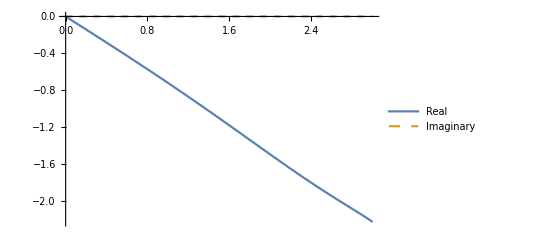

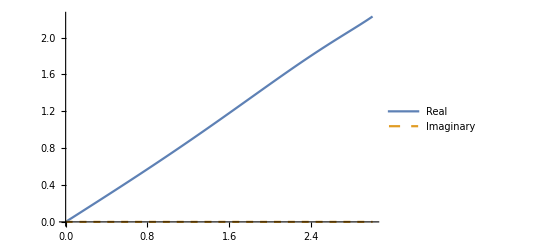

```mathematica
λex=Eigenvalues[Ω[[3]]];
Plot[
{Re[(λex/.{t->tp})[[1]]],Im[(λex/.{t->tp})[[1]]]},{tp,0,3},
PlotStyle->{Thick,Dashed},
PlotLegends->{"Real","Imaginary"}
]
Plot[
{Re[(λex/.{t->tp})[[2]]],Im[(λex/.{t->tp})[[1]]]},{tp,0,3},
PlotStyle->{Thick,Dashed},
PlotLegends->{"Real","Imaginary"}
]
```